# Geodesics Equation Solver

## Kerr’s Spacetime

## Manual calculation of the geodesics equations

```mathematica
Clear["Global`*"]
ClearAll[r,θ,ϕ,t,s]


ρ=r^2+a^2 Cos[θ]^2; 
Δ=r^2-2 m r+a^2;

(*Usual Boyer-Lindquist*)
(*metric={{-ρ/Δ,0,0,0},{0,-ρ,0,0},{0,0,-(((r^2+a^2)^2-Δ a Sin[θ]^2)/ρ) Sin[θ]^2,(a Sin[θ]^2( r^2 +a^2-Δ))/ρ},{0,0,(a Sin[θ]^2( r^2 +a^2-Δ))/ρ,(Δ-a^2 Sin[θ]^2)/ρ}};*)

(*From one of professors book*)
(*metric={{-ρ^2/Δ,0,0,0},{0,-ρ^2,0,0},{0,0,-(r^2+a^2) Sin[θ]^2-(2 m r a^2 Sin[θ]^4)/ρ^2,((2 m a r) Sin[θ]^2)/ρ^2},{0,0,((2 m a r) Sin[θ]^2)/ρ^2,1-(2 m r)/ρ^2}};*)

(*Eddington-Finkelstein*)
(*metric={{0,0,a Sin[θ]^2,-1},{0,-ρ^2,0,0},{a Sin[θ]^2,0,-(r^2+a^2) Sin[θ]^2-(2 m r a^2 Sin[θ]^4)/ρ^2,((2 m a r) Sin[θ]^2)/ρ^2},{-1,0,((2 m a r) Sin[θ]^2)/ρ^2,1-(2 m r)/ρ^2}}; *)
(* Com coordenadas (r,θ,ϕ,ν)*)


inversemetric = Simplify[Inverse[metric]];
coord={r,θ,ϕ,t};
christ[i_,j_,k_]:=christ[i,j,k]=Simplify[Sum[1/2 inversemetric[[i,d]] (D[metric[[d,k]],coord[[j]]]+D[metric[[d,j]],coord[[k]]]-D[metric[[j,k]],coord[[d]]]),{d,1,4}]]
```

```mathematica
eq=Table[coord[[i]]''+Sum[christ[i,j,k] coord[[j]]' coord[[k]]',{j,1,4},{k,1,4}],{i,1,4,1}];
eqs=eq/. {r''->r''[s],θ''->θ''[s],ϕ''->ϕ''[s],t''->t''[s],r'->r'[s],θ'->θ'[s],ϕ'->ϕ'[s],t'->t'[s],r->r[s],θ->θ[s],ϕ->ϕ[s],t->t[s]};
```

## Solving the equations

```mathematica
EQ=Table[eqs[[i]]==0/. {m->0.8,a->0.7},{i,1,4}];


Radius=2;
values ={};
sSingular=1000;
kerr=NDSolve[{EQ,
r[0]==3.5,θ[0]==Pi/2,t[0]==0,ϕ[0]==0,
r'[0]==-2,θ'[0]==0.05,t'[0]==0,ϕ'[0]==0.088
},
{r,θ,ϕ,t},
{s,0,sSingular},
Method->{"StiffnessSwitching"},MaxStepSize->0.01,
AccuracyGoal->10,PrecisionGoal->10,
StepMonitor :> AppendTo[values,{r[s],θ[s],ϕ[s],t[s]}]
];

{rFunc,θFunc,ϕFunc}={r,θ,ϕ}/. kerr[[1]];
domain=First@rFunc["Domain"]

m = 0.8;
a = 0.7;

trajectory=ParametricPlot3D[{Sqrt[a^2+rFunc[s]^2]*Sin[θFunc[s]]*Cos[ϕFunc[s]],Sqrt[a^2+rFunc[s]^2]*Sin[θFunc[s]]*Sin[ϕFunc[s]],rFunc[s]*Cos[θFunc[s]]},{s,0,domain[[2]]},ColorFunction->Hue,AxesLabel->{"x","y","z"},PlotRange->Automatic,RegionFunction->Function[{x,y,z,s},Sqrt[x^2+y^2+z^2]>10^-8],Exclusions->None];
```

{0.,1000.}

-Graphics3D-

-Graphics3D-

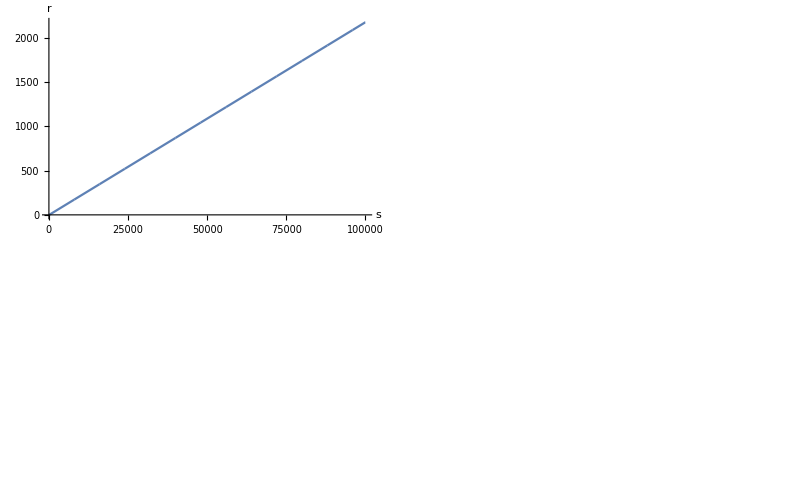

```mathematica
(*Kerr's black hole representation*)


(*Ring Singularity*)
Singularity = ParametricPlot3D[{a*Cos[ϕ],a*Sin[ϕ],0},{ϕ,0,2 Pi},PlotStyle->{Red}];

(*Infinite red shift surfaces*)
rSplus[θ_] := m+Sqrt[m^2-a^2 Cos[θ]^2];
rSminus[θ_] := m-Sqrt[m^2-a^2 Cos[θ]^2];

Ergosphere =ParametricPlot3D[{
{(Sqrt[rSplus[θ]^2+a^2] Sin[θ] Cos[φ]),(Sqrt[rSplus[θ]^2+a^2] Sin[θ] Sin[φ]),(rSplus[θ]Cos[θ])},(*Outer horizon*)
{(Sqrt[rSminus[θ]^2+a^2] Sin[θ] Cos[φ]),(Sqrt[rSminus[θ]^2+a^2] Sin[θ] Sin[φ]),(rSminus[θ]Cos[θ])}  (*Inner horizon*)
},
{θ,0,Pi},{φ,0,2 Pi},
PlotStyle->{Directive[Green,Opacity[0.1]],(*Outer horizon*)
		     Directive[Blue,Opacity[0.3]]    (*Inner horizon*)},
Mesh->None];

(*Event Horizons (2 if a^2<m^2) r_(+-)=r+-(m^2-a^2 cos^2 θ)^(1/2)*)
rHplus=m+Sqrt[m^2-a^2];
rHminus=m-Sqrt[m^2-a^2];

EventHorizon =ParametricPlot3D[{
{(Sqrt[rHplus^2+a^2] Sin[θ] Cos[φ]),(Sqrt[rHplus^2+a^2] Sin[θ] Sin[φ]),(rHplus *Cos[θ])},(*Outer horizon*)
{(Sqrt[rHminus^2+a^2] Sin[θ] Cos[φ]),(Sqrt[rHminus^2+a^2] Sin[θ] Sin[φ]),(rHminus*Cos[θ])}  (*Inner horizon*)
},
{θ,0,Pi},{φ,0,2 Pi},
PlotStyle->{Directive[Gray,Opacity[0.2]],(*Outer horizon*)
		     Directive[Gray,Opacity[0.5]]    (*Inner horizon*)},
Mesh->None];




Show[Singularity, EventHorizon, Ergosphere,PlotRange->All]

Show[trajectory,Singularity, EventHorizon, Ergosphere,PlotRange->Automatic]
(*{{-10,10},{-10,10},{-10,10}}*)

GraphicsGrid[{
{ListLinePlot[values[[All,1]],PlotRange->Automatic,AxesLabel->{"s","r"}],
ListLinePlot[values[[All,2]],PlotRange->All,AxesLabel->{"s","θ"}]
},{ListLinePlot[values[[All,3]],PlotRange->All,AxesLabel->{"s","ϕ"}],
ListLinePlot[values[[All,4]],PlotRange->All,AxesLabel->{"s","t"}]
}}]
```